# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Packages

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["Steiner`Utilities`", "packages\\steiner_utilities.wl"]
```

```mathematica
Needs["LeftistHeap`", "packages\\data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "packages\\steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "packages\\steiner_generator.wl"]
Needs["Steiner`SteinLib`", "packages\\steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "packages\\steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "packages\\steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Dijkstra`", "packages\\steiner_algorithms_dijkstra.wl"]
Needs["Steiner`Algorithms`Greedy`", "packages\\steiner_algorithms_greedy.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "packages\\steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "packages\\steiner_algorithms_approximation.wl"]
Needs["Steiner`Algorithms`LocalSearch`", "packages\\steiner_algorithms_local_search.wl"]
```

```mathematica
Needs["TestingSystem`", "packages\\testing_system.wl"]
```

## Input data

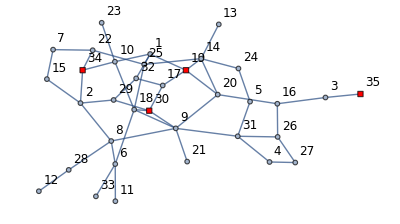

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstanceRG[35, 50, 4, WeightBounds ->{1, 1000}];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12],ImageSize->400]
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_15.mx", {graph15, weightAssociation15, terminals15}];
```

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
```

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstanceRG[150, 250, 20, WeightBounds ->{1, 1000}];
```

```mathematica
DumpSave[Directory[]~~"/dump/nice_100.mx", {graph100, weightAssociation100, terminals100}];
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
```

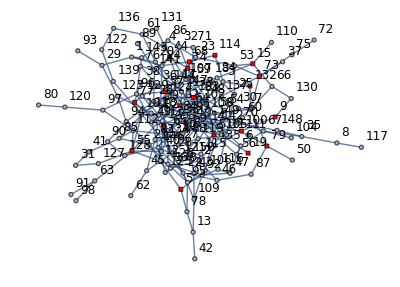

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

```mathematica
getInstancesList["\\steinlib\\D"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["\\steinlib\\D\\d15.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

5000

500

## Visualization Examples

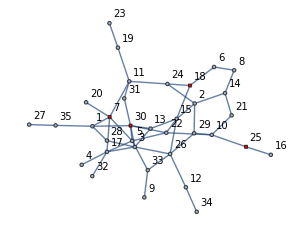

```mathematica
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,10]]
```

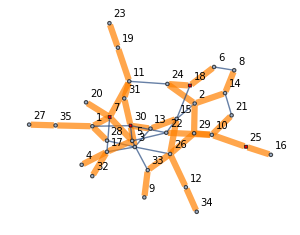

```mathematica
drawGraphSubgraph[graph15, FindSpanningTree[graph15]//EdgeList, terminals15, VertexLabelStyle->Directive[Black,10]]
```

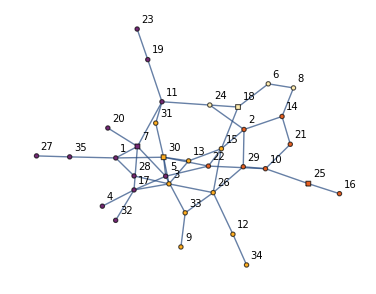

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]],
TerminalSize->0.65]
```

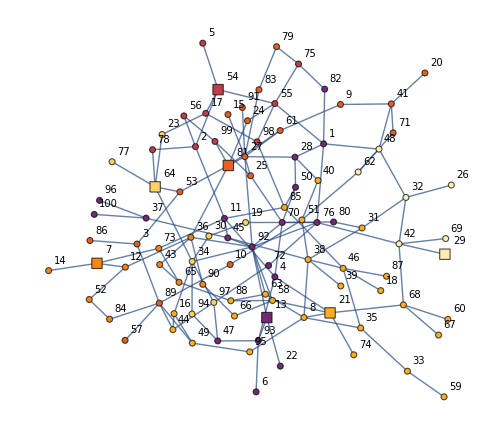

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

### Animation export

```mathematica
dijkstraVoronoi[graph15, terminals15];
voronoiVertexStyle[VertexList@graph15, Normal[%["voronoi"]]]⟦%["order"]⟧;
a = Table[
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧,
TerminalSize->0.65,
ImageSize->500]
,
{step, 1,VertexCount@graph15, 1}];
```

```mathematica
Export"visual/steiner_voronoi.gif", a, "GIF" , "ControlAppearance"->None,"DisplayDurations"->0.5,ImageSize->700];
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2), where t = #Terminals. n = #Vertices.

#### 15

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
resultDreyfusWagner15
```

{0.153892,Null}

1884.

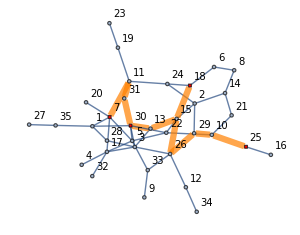
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884.

```mathematica
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

#### 100 Verts

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
resultDreyfusWagner100
```

{13.9607,Null}

5933.

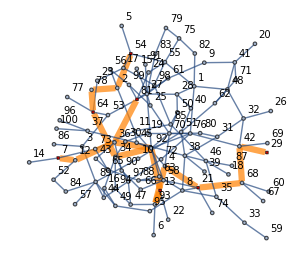
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 5933.

```mathematica
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

#### Stlib

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultDreyfusWagnerStlibTest
```

{0.0491777,Null}

7.

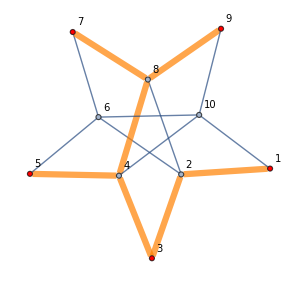
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7.

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

```mathematica
edgeWeightSum[Sort/@treeDreyfusWagnerStlibTest, stlibTestWeights]
```

7

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi separation of graph.
	- new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Refind original short-path graph accorgind to spanning tree.
4. Find MinSpanningTree in it.
5. Cut it, to make Steiner-tree.

### Examples

#### 15 Verts

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0785398,Null}

3848

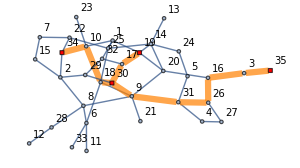
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 3848

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[treeMehlhorn15, weightAssociation15]
```

{0.862567,Null}

3321

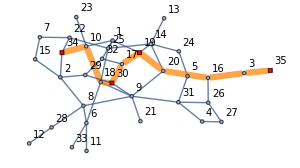
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 3321

```mathematica
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

#### 100 Verts

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{1.09714,Null}

18864

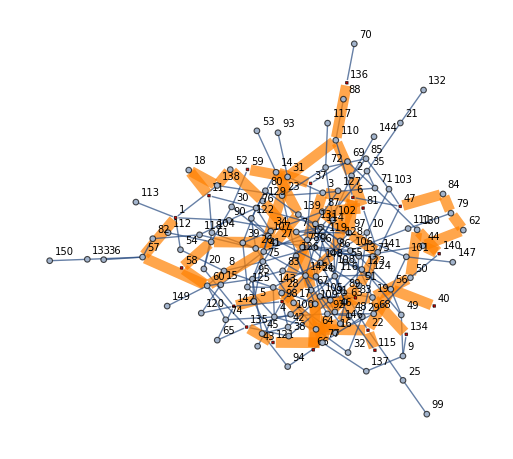
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16406

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{0.0258924,Null}

16083

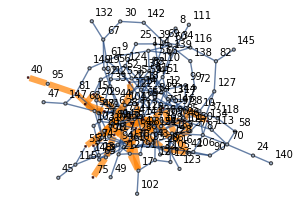
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 11711

```mathematica
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

#### Stlib

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[treeMehlhornStlibTest, stlibTestWeights]
```

{1.46374,Null}

1137

```mathematica
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest];
```

## Greedy algorithms [6][7]

### SPH

#### Description

Алгоритм начинает с заданного терминала, и добавляет в дерево текущий близжайший терминал (относительно всех вершин дерева) до тех пор, пока не добавит все терминалы .

### Repeated SPH

#### Description

SPH запускается заданное количество раз из случайного терминала (без повторов), затем берется лучший из результатов.

### Examples

{0.0205241,{3<->35,3<->16,16<->26,16<->20,26<->31,9<->31,8<->9,9<->30,2<->8,2<->34,19<->20}}

True

4495

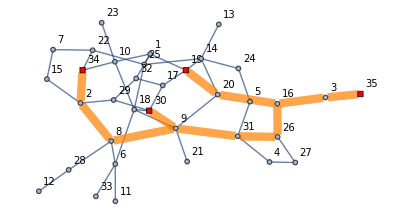
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 4495

```mathematica
(treeSP15 = steinerShortestPathHeuristic[graph15, terminals15, terminals15⟦1⟧])//AbsoluteTiming
steinerSolutionQ[treeSP15, terminals15]
resultSP15 = edgeWeightSum[graph15, treeSP15]
gridResult[graph15,  terminals15, treeSP15, resultSP15]
```

{0.0903438,{19<->20,16<->20,3<->16,16<->26,3<->35,26<->31,9<->31,8<->9,9<->30,2<->8,2<->34}}

4495

True

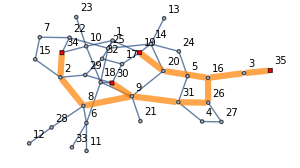
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 4495

```mathematica
(treeRSP15 = steinerRepeatedShortestPathHeuristic[graph15, terminals15, 100])//AbsoluteTiming
resultSP15 = edgeWeightSum[graph15, treeRSP15]
steinerSolutionQ[treeRSP15, terminals15]
gridResult[graph15,  terminals15, treeSP15, resultSP15]
```

{0.524759,Null}

True

20556

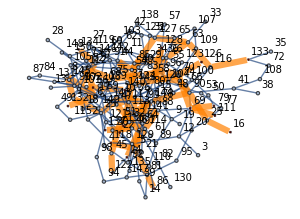
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 20556

```mathematica
(treeSP100 = steinerShortestPathHeuristic[graph100, terminals100, terminals100⟦20⟧]);//AbsoluteTiming
steinerSolutionQ[treeSP100, terminals100]
resultSP100 = edgeWeightSum[graph100, treeSP100]
gridResult[graph100,  terminals100, treeSP100, resultSP100]
```

{9.96847,Null}

True

18762

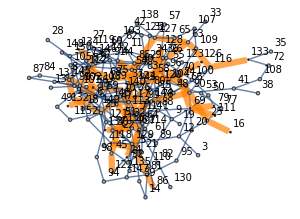
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 18762

```mathematica
(treeSP100 = steinerRepeatedShortestPathHeuristic[graph100, terminals100, 100]);//AbsoluteTiming
steinerSolutionQ[treeSP100, terminals100]
resultSP100 = edgeWeightSum[graph100, treeSP100]
gridResult[graph100,  terminals100, treeSP100, resultSP100]
```

## Local-search algorithms [7]

Для любого решения T задачи штейнера на графе (не обязательно оптимального) выполняется неравенство MST[V (T)] ≤ T.
Т.е. нахождением минимального остовного дерева набора вершин решения в графе, можно получить тривиальное улучшение решение.
И наоборот, для любого оптимального дерева штейнера должно выполнятся равенство.

### Steiner-Vertex Insertion

Steiner-vertex Insertion просматривает окрестность решений, отличающуюся от данного 1-ой добавленной вершиной, пересчитывает для элементов окрестности MST и проверяет, можно ли получить улучшение таким образом.

```mathematica
tree = steinerVertexInsertion[graph100, treeKouMarkowskyBerman100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{29<->42,42<->68,61<->81,27<->61,36<->81,34<->92,13<->92,34<->64,53<->64,64<->78,27<->53,13<->93,21<->68,4<->21,4<->93,2<->54,2<->78,7<->12,12<->36}

6444

6444

```mathematica
tree = steinerVertexInsertion[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1125

1137

```mathematica
tree = steinerVertexInsertionFixedPoint[stlibTestGraph, treeMehlhornStlibTest];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1124

1137

```mathematica
tree = steinerVertexInsertion[graph15, treeKouMarkowskyBerman15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{8<->24,10<->24,17<->27,27<->30,16<->30,2<->30,16<->18,10<->18}

3103

3103

### Speed-up

```mathematica
ClearAll[connectingEdgeQ, getConnectingEdges]

connectingEdgeQ[edge_, componentVertices_] :=Xor[MemberQ[componentVertices, First[edge]],MemberQ[componentVertices, Last[edge]]]

getConnectingEdges[edgeList_, componentVertices_] := Select[edgeList, connectingEdgeQ[#, componentVertices]&]
```

```mathematica
ClearAll[findExactEdgePath]

findExactEdgePath[edges_, v_, u_] := UndirectedEdge@@@Partition[FindPath[{1<->2, 2<->3}, 1,3, Infinity, 1]⟦1⟧, 2, 1]
```

```mathematica
ClearAll[steinerVertexInsertion]

steinerVertexInsertion::usage = "";
steinerVertexInsertion[graph_, tree_]:=
Block[{tryAddVertex},
Module[
{treeEdges = EdgeList@tree, treeVertices = VertexList@tree,
graphEdges = EdgeList@graph, graphVertices = VertexList@graph,
edgesByVertex},

edgesByVertex = getConnectingEdges[graphEdges, treeVertices];

(*tryAddVertex[]:=treeEdges;

Scan[
tryAddVertex[IncidenceList[edgesByVertex, #] ]
&,
Complement[graphVertices, treeVertices]]*)

]
]
```

### Steiner-Vertex Elimination

Steiner-vertex Elimination просматривает окрестность решений, отличающуюся от данного 1-ой удаленной вершиной штейнера, и для каждого элемента этой окрестности пересчитывает MST (если он связен), и проверяет, возможно ли улучшение решения.

```mathematica
resultDreyfusWagner15
resultDreyfusWagner100
```

1884.

5933.

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

True

1884

2173

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{9<->69,9<->89,16<->25,17<->102,17<->132,22<->129,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,48<->93,48<->104,51<->144,56<->112,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->116,90<->144,93<->120,96<->104,102<->143,110<->129,116<->133,117<->136,117<->143,118<->129,137<->149,139<->140}

True

17939

21343

```mathematica
tree = steinerVertexEliminationFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{22<->136,22<->121,117<->136,67<->134,67<->102,117<->143,85<->117,102<->143,17<->102,58<->128,26<->58,58<->74,26<->85,26<->120,5<->93,80<->93,93<->120,5<->118,5<->81,81<->86,86<->110,76<->80,47<->76,47<->97,47<->139,47<->56,24<->97,24<->122,139<->140,9<->69,69<->70,69<->79,69<->111,9<->89,89<->110,17<->132,121<->149,137<->149,16<->25,25<->90,74<->90,90<->116,116<->133,70<->96,70<->126}

True

16083

16083

```mathematica
tree = steinerVertexElimination[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1133

1137

### Speed-up

Это жесть, конечно, в WM писать. Но зато интересные структуры используются: левосторонние кучи, СНМ. Еще можно дописать нормальный поиск lca.

```mathematica
ClearAll[partialKruskal]

partialKruskal[pairsEdgeWeight_List, disj_] := 
Module[{edgeTaken=CreateDataStructure["Stack"]},

Scan[
If[!disj["CommonSubsetQ", First[#⟦1⟧], Last[#⟦1⟧]],
edgeTaken["Insert", #];
disj["Unify", First[#⟦1⟧], Last[#⟦1⟧]];]
&,
 SortBy[pairsEdgeWeight, Last]];

Normal@edgeTaken]
```

```mathematica
ClearAll[walkAndSet]

walkAndSet[graph_, start_, disj_] :=
DepthFirstScan[graph, start,
{"DiscoverVertex"->
((disj["Insert", #];disj["Unify", start, #];)&)}]
```

```mathematica
ClearAll[rootTree]

rootTree[tree_, graphVertexNumber_]:=
Module[{root, depth, parent, children},
root          = First[VertexList@tree];
depth        = CreateDataStructure["FixedArray", graphVertexNumber];
parent      = CreateDataStructure["FixedArray", graphVertexNumber];
children = CreateDataStructure["FixedArray", graphVertexNumber];
Scan[children["SetPart", #, CreateDataStructure["Stack"]]&, VertexList@tree];
DepthFirstScan[EdgeList@tree, root,
{"DiscoverVertex"->
((depth["SetPart", #1, #3];
If[#2≠#1, children["Part", #2]["Push", #1]];
parent["SetPart", #1, #2];)&)}];

{root, depth, parent, children}]
```

```mathematica
ClearAll[steinerVertexEliminationSpeedUp]

steinerVertexEliminationSpeedUp::usage = "";
steinerVertexEliminationSpeedUp[graph_, tree_, terminals_]:=
Block[
{dfs, lheap, lca, lcaUpwards},
With[{treeEdges = EdgeList@tree, treeVertices = VertexList@tree, treeVertexNumber = VertexCount@tree,
graphEdges = EdgeList@graph, graphVertices = VertexList@graph, graphVertNumber = VertexCount[graph]},
Module[
{graphTreeEdges, root,
lcaEdges, depth, parent, children, solution = {-1, treeEdges}},

(* graph rooting *)
{root, depth, parent, children} = rootTree[tree, graphVertNumber];

(* induced by current solution vertices subgraph's edges *)
graphTreeEdges = EdgeList@Subgraph[graph, treeVertices];

(* lca finding *)
lca[v_, u_]:=lcaUpwards[u,  Nest[parent["Part", #]&, v, depth["Part", v] - depth["Part", u]]];
lca[v_, u_]/;depth["Part", v] < depth["Part", u]:=lca[u, v];
lcaUpwards[v_, u_]:=lcaUpwards[parent["Part", v], parent["Part", u]];
lcaUpwards[v_, v_]:=v;

lcaEdges = CreateDataStructure["FixedArray", graphVertNumber];
Scan[lcaEdges["SetPart", #, CreateDataStructure["Stack"]]&, treeVertices];
Scan[lcaEdges["Part", lca[First[#], Last[#]]]["Push", {#, edgeWeight[graph, #]}]&, graphTreeEdges];
Print["Root:"];
Print[root];
Scan[(Print[ToString[#]~~": "];Print[Normal@lcaEdges["Part", #]])&, treeVertices];
(* main step *)
Block[{extractMinUntill, downUpEdgeQ},
Module[{disj,  edgesFinal = {}, mstDisj},
disj = CreateDataStructure["DisjointSet"];

downUpEdgeQ[v_, u_, disj_]:=Xor[disj["MemberQ", v], disj["MemberQ", u]];

extractMinUntill[heapID_]:=
NestWhile[
If[downUpEdgeQ[First@#, Last@#, disj]&[leftistHeapPeek[lheap[heapID]]],
leftistExtractMin[lheap[heapID]],
leftistExtractMin[lheap[heapID]];1]&,
1,
#==1&,
{2,1}];

dfs[v_]:=
Module[
{edgeCandidates, successors =  Normal@children["Part", v]},

If[!MatchQ[successors , {}],
Scan[dfs[#]&, successors];
edgeCandidates = Map[extractMinUntill[#]&, successors];
Print[v];
Print[edgeCandidates];
Print[Normal@lcaEdges["Part", v]];
edgeCandidates =
DeleteCases[
Join[{#, edgeWeight[graph, #]}&/@edgeCandidates, Normal@lcaEdges["Part", v]],
x_/;MemberQ[#, x⟦1⟧]]&[IncidenceList[graphTreeEdges, v]];
Print[edgeCandidates];

mstDisj = disj["Copy"];
If[parent["Part", v]≠v,
walkAndSet[VertexDelete[treeEdges, v], parent["Part", v], mstDisj];
];
(* СНМ !!!*)
edgesFinal = partialKruskal[edgeCandidates, mstDisj];

Sow[{v, edgeCandidates, Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]}];

If[FreeQ[terminals, v]∧
ConnectedGraphQ@Graph[Complement[treeVertices, {v}],Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]]∧Total[edgesFinal⟦All, 2⟧] < Total[edgeWeight[graph, #]&/@IncidenceList[treeEdges, v]],
solution = {v, Union[edgesFinal⟦All, 1⟧, Complement[treeEdges, IncidenceList[treeEdges, v]]]};];

disj["Insert", v];
Scan[disj["Unify", v, #]&, successors];
lheap[v]=leftistHeapHeapify[{#, edgeWeight[graph, #]}&/@Cases[IncidenceList[graphTreeEdges, v], x_/;Xor[disj["MemberQ", x⟦1⟧], disj["MemberQ", x⟦2⟧]]]];
Map[leftistHeapMeldClearly[lheap[v], lheap[#]]&, successors];

,

(* leaf *)
disj["Insert", v];
Print["Leaf:"];
Print[v];
Print[{IncidenceList[graphTreeEdges, v]}];
Print["end:"];
lheap[v]=leftistHeapHeapify[{#, edgeWeight[graph, #]}&/@IncidenceList[graphTreeEdges, v]];
];
];

dfs[root];
solution
];
];
]
]
]
```

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{0.0442199,Null}

6444

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0098035,Null}

2173

```mathematica
tree =  steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

34

{2<->54,2<->78,4<->21,4<->93,7<->12,12<->36,13<->92,13<->93,21<->68,27<->53,27<->61,27<->92,29<->42,36<->81,42<->68,53<->64,61<->81,64<->78}

6221

6444

```mathematica
treeTest =  steinerVertexElimination[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[treeTest, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

1884

2173

```mathematica
var = Reap[steinerVertexEliminationSpeedUp[graph15, treeKouMarkowskyBerman15, terminals15], _, First]⟦2, 1⟧
```

```mathematica
IncidenceList[treeKouMarkowskyBerman15, 10]
```

{10<->25,10<->29}

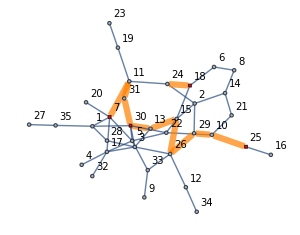
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

```mathematica
gridResult[graph15,  terminals15, {7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,18<->24,26<->29,30<->31}, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

```mathematica
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
```

2173

2173

```mathematica
steinerVertexEliminationSpeedUp[graph15, treeKouMarkowskyBerman15, terminals15]
tree =  %⟦2⟧;
%%⟦1⟧;
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
%%%%
```

```mathematica
t1 = steinerVertexEliminationFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100];//AbsoluteTiming
t2 = steinerVertexEliminationSpeedUp[graph100, treeKouMarkowskyBerman100, terminals100];//AbsoluteTiming
```

{0.0630061,Null}

{0.0346224,Null}

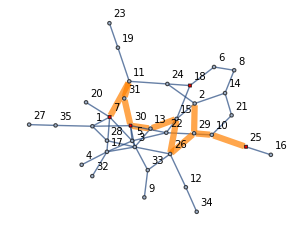
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1404

```mathematica
gridResult[graph15,  terminals15, tree, edgeWeightSum[graph15, tree]]
```

```mathematica
gridResult[graph15,  terminals15, treeTest, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

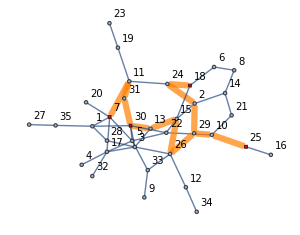
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, edgeWeightSum[graph15, treeKouMarkowskyBerman15]]
```

### VIVE

Vertex insertion, vertex elimination

```mathematica
tree =  steinerVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->18,15<->26,26<->29,30<->31}

True

1884

2173

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{9<->69,9<->89,16<->25,17<->102,17<->132,22<->113,22<->129,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->113,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->116,90<->144,93<->120,102<->143,110<->129,113<->140,116<->133,117<->136,117<->143,118<->129,137<->149,139<->140}

True

17075

21343

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeMehlhorn100, weightAssociation100]
```

{22<->136,22<->121,117<->136,67<->134,67<->102,117<->143,85<->117,102<->143,17<->102,58<->128,26<->58,58<->74,26<->85,26<->120,5<->93,80<->93,93<->120,5<->118,5<->81,81<->86,86<->110,76<->80,47<->76,47<->97,47<->139,47<->56,24<->97,24<->122,139<->140,9<->69,69<->70,69<->79,69<->111,9<->89,89<->110,17<->132,121<->149,137<->149,16<->25,25<->90,74<->90,90<->116,116<->133,70<->96,70<->126}

True

16083

16083

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[tree, weightAssociation100]
edgeWeightSum[treeSP100, weightAssociation100]
```

{1<->8,1<->23,5<->81,5<->93,5<->118,8<->102,10<->23,10<->93,16<->25,17<->102,17<->132,22<->113,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->83,75<->113,75<->149,76<->80,80<->93,81<->86,83<->96,85<->117,90<->116,90<->144,93<->120,113<->140,116<->133,117<->136,137<->149,139<->140}

True

16725

18762

```mathematica
tree = steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
Total[edgeWeight[stlibTestGraph, #]&/@tree]
Total[edgeWeight[stlibTestGraph, #]&/@treeMehlhornStlibTest]
```

1120

1137

### Key-Path Exchange

#### Description

```mathematica
-Graphics-
-Graphics-
```

#### Examples

```mathematica
ClearAll[crucialQ]

crucialQ[v_, tree_, terminals_]:=(VertexDegree[tree, v]≥3)∨((*VertexDegree[tree, v] == 2 ∧*)MemberQ[terminals, v])
```

```mathematica
ClearAll[rootTree]

rootTree[tree_, graphVertexNumber_, terminals_]:=
Module[{root, depth, parent, children},
root          = FirstCase[VertexList@tree, x_/;crucialQ[x, tree, terminals]];
depth        = CreateDataStructure["FixedArray", graphVertexNumber];
parent      = CreateDataStructure["FixedArray", graphVertexNumber];
children = CreateDataStructure["FixedArray", graphVertexNumber];
Scan[children["SetPart", #, CreateDataStructure["Stack"]]&, VertexList@tree];
DepthFirstScan[EdgeList@tree, root,
{"DiscoverVertex"->
((depth["SetPart", #1, #3];
If[#2≠#1, children["Part", #2]["Push", #1]];
parent["SetPart", #1, #2];)&)}];

{root, depth, parent, children}]
```

```mathematica
ClearAll[steinerKeyPathExchange]

steinerKeyPathExchange::usage = "";
steinerKeyPathExchange[graph_, tree_, terminals_]:=
Block[{lheap, dfs, tryEliminatePath,
extractMinUntill,downUpEdgeQ,currentInternalKeyPath},
currentInternalKeyPath = CreateDataStructure["Stack"];
With[{treeVertexNumber = VertexCount@tree, graphVertexNumber=VertexCount@graph,
treeEdges = EdgeList@tree, graphEdges = EdgeList@graph, graphVertices = VertexList@graph, treeVertices = VertexList@tree},
Module[{voronoi, dist, anc, cent, heapArray, solution,
root, depth, parent, children,graphTreeEdges, disj,
baseBoundaryEdges, eliminatedPath},

solution = treeEdges;
graphTreeEdges = EdgeList@Subgraph[graph, treeVertices];

(* voronoi *)
voronoi = dijkstraVoronoi[graph, treeVertices];
anc = voronoi["ancestors"];
dist = voronoi["distance"];
cent = voronoi["voronoi"];

(* boundary edges push to heaps *)
baseBoundaryEdges = Select[graphEdges, cent["Part", First[#]] ≠ cent["Part", Last[#]]&];
Scan[(lheap[#]=leftistHeapCreate[])&, treeVertices];
Scan[
(leftistHeapPush[lheap[cent["Part", First[#]]], {#, dist["Part", First[#]] + dist["Part", Last[#]] + edgeWeight[graph, #]}];
leftistHeapPush[lheap[cent["Part", Last[#]]], {#, dist["Part", First[#]] + dist["Part", Last[#]] + edgeWeight[graph, #]}];)&,
baseBoundaryEdges ];

(* tree rooting *)
{root, depth, parent, children} = rootTree[tree, graphVertexNumber, terminals];
Sow[root, "root"];
Sow[children, "children"];
Sow[parent, "parent"];
Sow[cent, "center"];

disj = CreateDataStructure["DisjointSet"];
Scan[disj["Insert", #]&, treeVertices];

downUpEdgeQ[v_, u_, down_, disj_]:=
And[Xor[disj["CommonSubsetQ", cent["Part", v], down], disj["CommonSubsetQ", cent["Part", u], down]],
And[FreeQ[Normal@currentInternalKeyPath, cent["Part", v]], FreeQ[Normal@currentInternalKeyPath, cent["Part", u]]]];

extractMinUntill[heapID_]:=
NestWhile[
leftistExtractMin[lheap[heapID]]&,
Null,
!MatchQ[#, Null]∧!downUpEdgeQ[cent["Part", First@#], cent["Part", Last@#], heapID, disj]&,
{2,1}];

tryEliminatePath[path_, u_, v_]:=
Module[{edgeBase, , brokenTree, tabuVertices,
baseBit, bottomTree, upperTree, deletedZones, boundaryEdges, paths},
brokenTree=VertexDelete[treeEdges, Normal@currentInternalKeyPath];
bottomTree = First@ConnectedGraphComponents[brokenTree, u];
upperTree = First@ConnectedGraphComponents[brokenTree, v];

edgeBase = extractMinUntill[u];

deletedZones = Map[If[MemberQ[Normal@currentInternalKeyPath, cent["Part", #]], #,Nothing]&, graphVertices];
boundaryEdges = Select[baseBoundaryEdges,
Xor[
MemberQ[deletedZones, cent["Part", First[#]]],
MemberQ[deletedZones, cent["Part", Last[#]]]]&];

paths = DeleteCases[
{voronoiBoundaryPath[edgeBase, anc, cent],
repairVoronoi[graph, terminals, Normal@currentInternalKeyPath, dist, anc, cent, boundaryEdges, disj, u]},
Null];

Sow[path, "keyPath"];

If[!MatchQ[paths, {}], 
paths = MinimalBy[paths, edgeWeightSum[graph, #]&]⟦1⟧;
Print["Best of 2: "];
Print[paths];
If[edgeWeightSum[graph, paths]< edgeWeightSum[graph, path],
solution = Join[Complement[treeEdges, path, SameTest->(ContainsExactly[List@@#1, List@@#2]&)], paths];
eliminatedPath = {paths, path};
Print["New Solution: "];
Print[paths];
];
];

tabuVertices = Join[VertexList@bottomTree, Normal@currentInternalKeyPath];

];

dfs[v_]:=
Module[{successors = Normal@children["Part", v], prevCrus, path},
Sow[v, "visiting"];
Sow[successors, "suc"];
prevCrus = -1;
path = {};
Scan[Function[child,
({prevCrus, path} = dfs[child];
Switch[{prevCrus, crucialQ[v, treeEdges, terminals]},
{-1, _}, Nothing,
{_Integer, True},
(Sow["End: "~~ToString[v], "keyPathSeq"];
tryEliminatePath[path, prevCrus, v];Map[leftistHeapMeldClearly[lheap[v], lheap[#]]&, Normal@currentInternalKeyPath];
currentInternalKeyPath["DropAll"];),
_, Nothing];

disj["Unify", v, #];)

][#]&,
successors];

Which[
crucialQ[v, treeEdges, terminals], (Sow["Start: "~~ToString[v], "keyPathSeq"];{v, {UndirectedEdge@@Sort[{v, parent["Part", v]}]}}),
(Length@successors == 1 ∧ !MatchQ[prevCrus, -1]), (currentInternalKeyPath["Push", v]; Sow["Pass: "~~ToString[v]~~" to "~~ToString[parent["Part", v]], "keyPathSeq"];{prevCrus, Append[path, UndirectedEdge@@Sort[{v, parent["Part", v]}]]}),
True, {-1, {}}
]
];

dfs[root];
solution

]
]
]
```

```mathematica
ClearAll[steinerKeyPathExchangeFixedPoint]

steinerKeyPathExchangeFixedPoint::usage = "";
steinerKeyPathExchangeFixedPoint[graph_, tree_, terminals_]:= FixedPoint[steinerKeyPathExchange[graph, #, terminals]&, tree]
```

```mathematica
Complement[{1<->2}, {2<->1}, SameTest->(ContainsExactly[List@@#1, List@@#2]&)]
```

{}

```mathematica
<<(Directory[]~~"/dump/nice_100.mx")
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[treeKouMarkowskyBerman100, weightAssociation100]
```

{1.01097,Null}

21343

```mathematica
<<(Directory[]~~"/dump/nice_15.mx")
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

{0.0078188,Null}

2173

```mathematica
treeKouMarkowskyBerman15
```

{7<->11,11<->31,30<->31,13<->30,18<->24,13<->15,15<->26,2<->24,10<->25,10<->29,26<->29,2<->29}

```mathematica
steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15]
```

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,18<->15}

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,18<->15}

```mathematica
tree =  steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

Best of 2:

{10<->29,25<->10}

Best of 2:

{15<->18}

New Solution:

{15<->18}

Best of 2:

{11<->24}

Best of 2:

{11<->31,7<->11,30<->31}

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,15<->18}

1884

2173

```mathematica
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
gridResult[graph15,  terminals15, tree, edgeWeightSum[graph15, tree]]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 2173

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884

```mathematica
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1884.

```mathematica
tree =  steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15]
edgeWeightSum[tree, weightAssociation15]
edgeWeightSum[treeKouMarkowskyBerman15, weightAssociation15]
```

Base path:

Null

New path:

{10<->29,25<->10}

Best of 2:

{10<->29,25<->10}

Base path:

{15<->18}

New path:

{11<->24,18<->24}

Best of 2:

{15<->18}

New Solution:

{15<->18}

Base path:

{11<->24}

New path:

{2<->15,30<->13,13<->15}

Best of 2:

{11<->24}

Base path:

{1<->7,1<->30}

New path:

{11<->31,7<->11,30<->31}

Best of 2:

{11<->31,7<->11,30<->31}

{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,15<->18}

1884

2173

```mathematica
tree =  steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeKouMarkowskyBerman100]
```

New Solution:

{22<->121,121<->149}

New Solution:

{118<->129}

New Solution:

{24<->122}

New Solution:

{5<->93,5<->81,81<->86}

New Solution:

{90<->116,133<->116}

New Solution:

{69<->79}

New Solution:

{48<->93}

New Solution:

{47<->56}

New Solution:

{22<->121,121<->149}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149}

True

20721

21343

```mathematica
IncidenceList[graph100, 97]
```

{24<->97,47<->97,78<->97,82<->97,97<->117}

```mathematica
Position[Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"center"}]⟦2,1,1,1⟧//Normal, 97]
```

{{78},{82},{97},{130}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"vorRepParams"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{{},{}},{{97},{}},{{139},{}},{{76,80},{}},{{129},{}},{{2},{}},{{10},{}},{{120},{}},{{45,51,144},{}},{{25},{}},{{74},{}},{{},{}},{{},{}},{{85},{}},{{17},{}},{{67},{}},{{},{}},{{},{}},{{},{}},{{110,89,9},{}},{{},{}},{{},{}},{{116,63,127,54,44,124},{}},{{},{}},{{50,100,48,104},{}},{{83},{}},{{112},{}},{{},{}},{{18,59},{}},{{},{}}}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"vVerts"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{},97,78,{},139,37,142,{},80,76,64,36,21,{},129,30,92,{},2,{},10,{},120,{},45,144,6,71,66,51,{},25,12,77,{},74,{},{},{},85,103,{},17,7,68,106,131,84,{},67,105,{},{},{},{},9,110,89,{},{},{},124,116,63,15,119,125,54,42,127,138,{},{},50,104,48,34,55,53,{},83,{},112,91,145,148,{},{},59,18,{},{}}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"swap"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{swapped,24,97},{proc,97,24},{swapped,47,97},{proc,97,47},{swapped,58,78},{proc,78,58},{proc,78,104},{proc,97,117},{swapped,6,139},{proc,139,6},{swapped,27,142},{proc,142,27},{proc,37,88},{swapped,47,139},{proc,139,47},{swapped,73,139},{proc,139,73},{proc,139,140},{swapped,17,76},{proc,76,17},{proc,21,92},{proc,36,65},{proc,36,128},{swapped,46,76},{proc,76,46},{swapped,47,76},{proc,76,47},{swapped,51,64},{proc,64,51},{swapped,58,76},{proc,76,58},{proc,76,104},{proc,80,83},{proc,80,93},{swapped,4,92},{proc,92,4},{swapped,12,129},{proc,129,12},{swapped,21,92},{proc,92,21},{swapped,22,129},{proc,129,22},{swapped,23,129},{proc,129,23},{proc,30,143},{swapped,81,92},{proc,92,81},{swapped,110,129},{proc,129,110},{swapped,118,129},{proc,129,118},{proc,2,23},{proc,2,102},{proc,2,118},{proc,10,23},{proc,10,43},{proc,10,68},{proc,10,93},{swapped,26,120},{proc,120,26},{swapped,93,120},{proc,120,93},{proc,120,144},{proc,6,139},{proc,6,145},{proc,45,122},{proc,51,64},{proc,66,116},{proc,71,88},{proc,71,121},{proc,71,140},{swapped,90,144},{proc,144,90},{swapped,120,144},{proc,144,120},{swapped,141,144},{proc,144,141},{swapped,143,144},{proc,144,143},{proc,12,69},{proc,12,129},{swapped,16,25},{proc,25,16},{proc,25,90},{swapped,53,77},{proc,77,53},{swapped,58,74},{proc,74,58},{proc,74,90},{swapped,26,85},{proc,85,26},{swapped,55,85},{proc,85,55},{swapped,60,103},{proc,103,60},{swapped,67,85},{proc,85,67},{proc,85,117},{proc,7,140},{swapped,10,68},{proc,68,10},{proc,17,76},{proc,17,102},{proc,17,132},{swapped,60,106},{proc,106,60},{proc,84,145},{swapped,99,131},{proc,131,99},{proc,106,121},{proc,67,85},{proc,67,91},{proc,67,102},{proc,67,134},{swapped,99,105},{proc,105,99},{proc,9,15},{proc,9,69},{swapped,46,89},{proc,89,46},{swapped,86,110},{proc,110,86},{proc,110,129},{swapped,9,15},{proc,15,9},{swapped,23,124},{proc,124,23},{swapped,26,63},{proc,63,26},{swapped,29,125},{proc,125,29},{proc,42,60},{swapped,52,54},{proc,54,52},{proc,54,93},{swapped,57,127},{proc,127,57},{swapped,62,138},{proc,138,62},{swapped,65,127},{proc,127,65},{swapped,66,116},{proc,116,66},{swapped,70,124},{proc,124,70},{swapped,90,116},{proc,116,90},{swapped,91,119},{proc,119,91},{proc,116,133},{proc,119,150},{swapped,11,34},{proc,34,11},{proc,34,40},{proc,34,128},{proc,48,93},{proc,50,69},{proc,50,79},{proc,53,77},{proc,55,85},{swapped,76,104},{proc,104,76},{swapped,78,104},{proc,104,78},{swapped,96,104},{proc,104,96},{proc,104,123},{swapped,75,83},{proc,83,75},{swapped,80,83},{proc,83,80},{proc,83,96},{swapped,6,145},{proc,145,6},{swapped,29,91},{proc,91,29},{swapped,52,145},{proc,145,52},{swapped,56,112},{proc,112,56},{swapped,67,91},{proc,91,67},{swapped,75,91},{proc,91,75},{swapped,75,112},{proc,112,75},{swapped,84,145},{proc,145,84},{proc,91,119},{swapped,101,145},{proc,145,101},{proc,148,150},{proc,18,149},{proc,59,75},{proc,59,140},{proc,59,143}}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"vEdge"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{},24<->97,47<->97,78<->97,82<->97,97<->117,58<->78,78<->97,78<->104,82<->97,82<->130,82<->130,{},6<->139,37<->139,47<->139,73<->139,139<->140,37<->88,37<->139,37<->142,27<->142,37<->142,{},36<->80,64<->80,76<->80,80<->83,80<->93,17<->76,46<->76,47<->76,58<->76,76<->80,76<->104,21<->64,51<->64,64<->80,21<->64,21<->92,36<->65,36<->80,36<->128,{},12<->129,22<->129,23<->129,30<->129,92<->129,110<->129,118<->129,129<->135,129<->135,30<->129,30<->143,4<->92,21<->92,81<->92,92<->129,{},2<->23,2<->102,2<->118,{},10<->23,10<->43,10<->68,10<->93,{},26<->120,93<->120,120<->144,{},45<->51,45<->122,51<->144,66<->144,71<->144,90<->144,120<->144,141<->144,143<->144,6<->51,45<->51,51<->64,51<->144,6<->51,6<->139,6<->145,61<->71,71<->88,71<->121,71<->140,71<->144,66<->116,66<->144,61<->71,{},12<->25,16<->25,25<->77,25<->90,3<->12,12<->25,12<->69,12<->129,3<->12,25<->77,53<->77,{},58<->74,74<->90,{},{},{},26<->85,55<->85,67<->85,85<->103,85<->117,60<->103,85<->103,{},7<->17,17<->76,17<->102,17<->106,17<->132,7<->17,7<->131,7<->140,10<->68,68<->106,17<->106,60<->106,68<->106,106<->121,7<->131,87<->131,99<->131,84<->87,87<->131,84<->87,84<->145,{},67<->85,67<->91,67<->102,67<->105,67<->134,67<->105,99<->105,{},{},{},{},9<->15,9<->69,9<->89,9<->89,46<->89,89<->110,86<->110,89<->110,110<->129,{},{},{},23<->124,44<->124,70<->124,63<->116,66<->116,90<->116,116<->133,26<->63,33<->63,63<->116,63<->127,33<->63,9<->15,15<->54,44<->119,91<->119,119<->150,29<->125,42<->125,44<->54,44<->119,44<->124,15<->54,44<->54,52<->54,54<->93,54<->127,42<->127,54<->127,57<->127,63<->127,65<->127,127<->138,42<->60,42<->125,42<->127,62<->138,127<->138,{},{},50<->69,50<->79,50<->100,34<->104,48<->104,53<->104,76<->104,78<->104,96<->104,104<->123,48<->93,48<->100,48<->104,11<->34,34<->40,34<->104,34<->128,55<->85,55<->100,48<->100,50<->100,55<->100,53<->77,53<->104,{},75<->83,80<->83,83<->96,{},56<->112,75<->112,91<->112,112<->145,112<->148,29<->91,67<->91,75<->91,91<->112,91<->119,6<->145,52<->145,84<->145,101<->145,112<->145,112<->148,148<->150,{},{},18<->59,59<->75,59<->140,59<->143,18<->59,18<->149,{},{}}}}}

```mathematica
res =Normal@Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"center"}]⟦2,1,1, 1⟧
```

{102,2,25,23,93,51,17,102,9,10,90,25,102,93,54,16,17,18,69,90,80,22,23,24,25,26,102,102,90,129,90,140,63,104,133,80,139,133,93,140,133,127,58,44,45,136,47,48,23,50,51,102,104,54,100,56,128,58,59,102,144,75,63,80,26,144,67,17,69,70,144,133,102,74,75,76,25,97,79,80,86,97,83,17,85,86,17,69,89,90,112,129,93,86,86,96,97,22,23,100,143,102,85,104,67,17,26,133,70,110,111,112,22,22,23,116,117,118,44,120,22,122,26,124,127,126,127,128,129,97,17,132,133,134,129,136,137,127,139,140,22,139,143,144,112,90,86,112,149,102}

```mathematica
Reap[steinerKeyPathExchange[graph15, treeKouMarkowskyBerman15, terminals15], {"newEdge"}]
```

{{7<->11,10<->25,10<->29,11<->31,13<->15,13<->30,15<->26,26<->29,30<->31,15<->18},{{{{10<->29,25<->10},{11<->24,18<->24},{2<->15,30<->13,13<->15},{11<->31,7<->11,30<->31}}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"vorRep"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{},{24<->97,47<->97,58<->78,78<->104,97<->117},{6<->139,27<->142,37<->88,47<->139,73<->139,139<->140},{17<->76,21<->92,36<->65,36<->128,46<->76,47<->76,51<->64,58<->76,76<->104,80<->83,80<->93},{4<->92,12<->129,21<->92,22<->129,23<->129,30<->143,81<->92,110<->129,118<->129},{2<->23,2<->102,2<->118},{10<->23,10<->43,10<->68,10<->93},{26<->120,93<->120,120<->144},{6<->139,6<->145,45<->122,51<->64,66<->116,71<->88,71<->121,71<->140,90<->144,120<->144,141<->144,143<->144},{12<->69,12<->129,16<->25,25<->90,53<->77},{58<->74,74<->90},{},{},{26<->85,55<->85,60<->103,67<->85,85<->117},{7<->140,10<->68,17<->76,17<->102,17<->132,60<->106,84<->145,99<->131,106<->121},{67<->85,67<->91,67<->102,67<->134,99<->105},{},{},{},{9<->15,9<->69,46<->89,86<->110,110<->129},{},{},{9<->15,23<->124,26<->63,29<->125,42<->60,52<->54,54<->93,57<->127,62<->138,65<->127,66<->116,70<->124,90<->116,91<->119,116<->133,119<->150},{},{11<->34,34<->40,34<->128,48<->93,50<->69,50<->79,53<->77,55<->85,76<->104,78<->104,96<->104,104<->123},{75<->83,80<->83,83<->96},{6<->145,29<->91,52<->145,56<->112,67<->91,75<->91,75<->112,84<->145,91<->119,101<->145,148<->150},{},{18<->149,59<->75,59<->140,59<->143},{}}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"newEdge"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,47<->56},{{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}}}

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"pathCosts"}]
```

{9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,129<->118}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,24<->122}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,69<->79}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,93<->48}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,47<->56}

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,47<->56},{{{{{117<->136},214,214},{{24<->97,47<->97},433,796},{{139<->140,47<->139},444,446},{{47<->76,76<->80,80<->93},194,763},{{22<->129,23<->129},816,846},{{2<->118,2<->23},1309,877},{{10<->23,10<->93},375,728},{{93<->120,26<->120},338,580},{{45<->122,45<->51,51<->144,90<->144},1150,796},{{74<->90,58<->74},377,564},{{58<->128},12,12},{{26<->58},321,321},{{26<->85,85<->117},210,554},{{102<->143},157,157},{{137<->149},479,479},{{70<->126},641,641},{{69<->111},210,210},{{69<->70},161,161},{{70<->96},349,349},{{50<->79,50<->100,48<->100,48<->104,96<->104},2269,691},{{83<->96,75<->83},765,580},{{56<->112,75<->112},907,763},{{75<->149},397,397},{{117<->143},240,240}}}}}

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"visiting"}]
```

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,18<->59,18<->149,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,59<->143,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->112,75<->149,76<->80,80<->93,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,96<->104}

{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149}

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,137<->149},{{{117,136,85,26,120,93,80,76,47,97,24,139,140,10,23,129,22,2,118,58,74,90,144,51,45,122,25,16,128,143,102,17,132,67,134,59,18,149,137,75,83,96,70,126,69,9,89,110,86,111,124,44,54,127,63,116,133,104,48,100,50,79,112,56}}}}

```mathematica
res = Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"root", "keyPath", "suc", "children", "parent"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{117}},{{{117<->136},{24<->97,47<->97},{139<->140,47<->139},{47<->76,76<->80,80<->93},{22<->129,23<->129},{2<->118,2<->23},{10<->23,10<->93},{93<->120,26<->120},{45<->122,45<->51,51<->144,90<->144},{16<->25,25<->90},{74<->90,58<->74},{58<->128},{26<->58},{26<->85,85<->117},{17<->132,17<->102},{67<->134,67<->102},{102<->143},{137<->149},{70<->126},{86<->110,89<->110,9<->89,9<->69},{69<->111},{69<->70},{116<->133,63<->116,63<->127,54<->127,44<->54,44<->124,70<->124},{70<->96},{50<->79,50<->100,48<->100,48<->104,96<->104},{83<->96,75<->83},{56<->112,75<->112},{75<->149},{18<->149,18<->59,59<->143},{117<->143}}},{{{136,85,143},{},{26},{120,58},{93},{80,10},{76},{47},{97,139},{24},{},{140},{},{23},{129,2},{22},{},{118},{},{74,128},{90},{144,25},{51},{45},{122},{},{16},{},{},{102,59},{17,67},{132},{},{134},{},{18},{149},{137,75},{},{83,112},{96},{70,104},{126,69,124},{},{9,111},{89},{110},{86},{},{},{44},{54},{127},{63},{116},{133},{},{48},{100},{50},{79},{},{56},{}}},{{DataStructure[FixedArray, {Data -> {Null, DataStructure[Stack, {Data -> {118}}], Null, Null, Null, Null, Null, Null, DataStructure[Stack, {Data -> {89}}], DataStructure[Stack, {Data -> {23}}], Null, Null, Null, Null, Null, <<127>>, DataStructure[Stack, {Data -> <<1>>}], DataStructure[Stack, {Data -> {51}}], Null, Null, Null, Null, DataStructure[Stack, {Data -> {137, 75}}], Null}}]}},{{DataStructure[FixedArray, {Data -> {Null, 23, Null, Null, Null, Null, Null, Null, 69, 93, Null, Null, Null, Null, Null, 25, 102, 59, Null, Null, Null, 129, 10, 97, 90, 85, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, Null, <<88>>, Null, Null, 17, 116, 67, Null, 117, 149, Null, 47, 139, Null, Null, 117, 90, Null, Null, Null, Null, 18, Null}}]}}}}

```mathematica
Reap[steinerKeyPathExchange[graph100, treeKouMarkowskyBerman100, terminals100], {"vorRepParams"}]
```

{{2<->23,2<->118,9<->69,9<->89,10<->23,10<->93,16<->25,17<->102,17<->132,22<->129,23<->129,24<->97,25<->90,26<->58,26<->85,26<->120,44<->54,44<->124,45<->51,45<->122,47<->76,47<->97,47<->139,48<->100,48<->104,50<->79,50<->100,51<->144,54<->127,56<->112,58<->74,58<->128,63<->116,63<->127,67<->102,67<->134,69<->70,69<->111,70<->96,70<->124,70<->126,74<->90,75<->83,75<->112,75<->149,76<->80,80<->93,83<->96,85<->117,86<->110,89<->110,90<->144,93<->120,96<->104,102<->143,116<->133,117<->136,117<->143,137<->149,139<->140,22<->121,121<->149},{{{{{97},{78,82,130}},{{97},{82,130}},{{139},{37,142}},{{139},{142}},{{139},{}},{{76,80},{21,36,64,76}},{{76,80},{21,36,64}},{{76,80},{21,36}},{{76,80},{21}},{{76,80},{}},{{129},{30,92,135}},{{129},{92,135}},{{129},{135}},{{2},{}},{{10},{}},{{120},{}},{{45,51,144},{6,51,61,66,71,144}},{{45,51,144},{6,51,61,66,71}},{{45,51,144},{51,61,66,71}},{{45,51,144},{51,61,66}},{{45,51,144},{51,61}},{{45,51,144},{61}},{{25},{3,12,77}},{{25},{3,77}},{{25},{3}},{{74},{}},{{85},{103}},{{85},{}},{{17},{7,68,84,87,106,131}},{{17},{68,84,87,106,131}},{{17},{84,87,106,131}},{{17},{84,87,131}},{{17},{84,87}},{{17},{87}},{{67},{105}},{{67},{}},{{110,89,9},{89,110}},{{110,89,9},{89}},{{110,89,9},{}},{{116,63,127,54,44,124},{15,33,42,44,54,63,116,119,125,127,138}},{{116,63,127,54,44,124},{15,33,42,44,54,63,119,125,127,138}},{{116,63,127,54,44,124},{15,33,42,44,54,119,125,127,138}},{{116,63,127,54,44,124},{33,42,44,54,119,125,127,138}},{{116,63,127,54,44,124},{33,42,44,54,125,127,138}},{{116,63,127,54,44,124},{33,42,44,54,127,138}},{{116,63,127,54,44,124},{33,42,44,127,138}},{{116,63,127,54,44,124},{33,44,127,138}},{{116,63,127,54,44,124},{33,44,138}},{{116,63,127,54,44,124},{33,44}},{{50,100,48,104},{34,48,53,55,100,104}},{{50,100,48,104},{34,48,53,55,100}},{{50,100,48,104},{34,53,55,100}},{{50,100,48,104},{53,55,100}},{{50,100,48,104},{53,100}},{{50,100,48,104},{100}},{{83},{}},{{112},{91,145,148}},{{112},{145,148}},{{112},{148}},{{112},{}},{{18,59},{18}},{{18,59},{}}}}}}

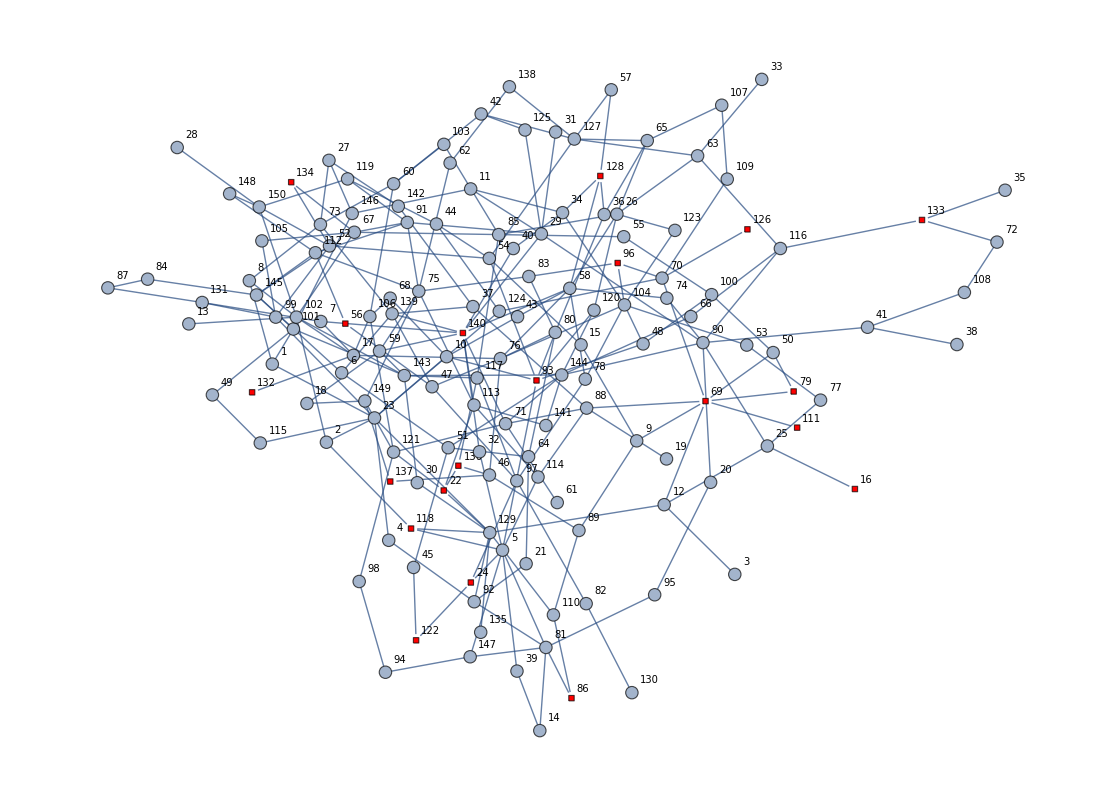

```mathematica
drawGraph[graph100, terminals100]
```

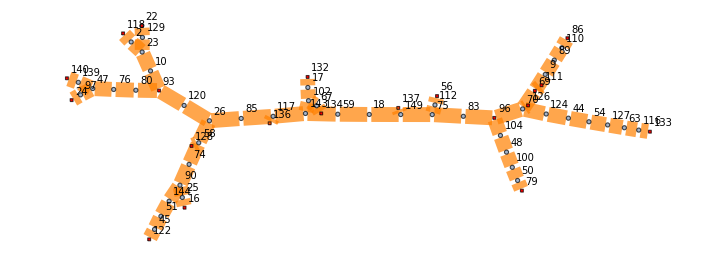
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 21343

```mathematica
gridResult[Graph@treeKouMarkowskyBerman100,  terminals100, Flatten@res⟦2,2,1⟧, edgeWeightSum[graph100, treeKouMarkowskyBerman100]]
```

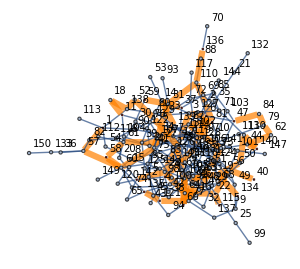
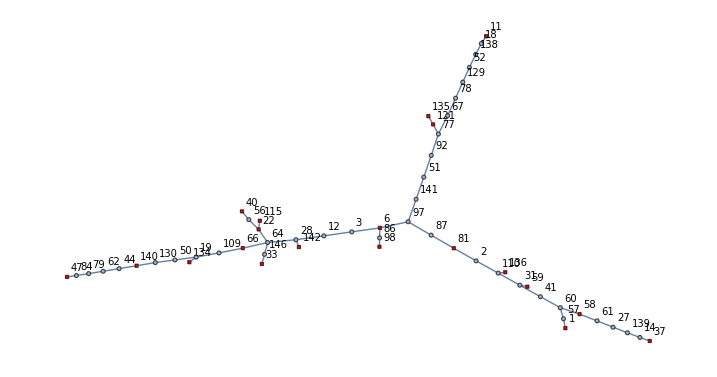
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 16406

```mathematica
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, edgeWeightSum[graph100, treeKouMarkowskyBerman100]]
```

```mathematica
{{{2<->110,2<->81,81<->87,87<->97},6<->110,6,110,{6<->110}},{{77<->92,51<->92,51<->141,97<->141},121<->77,121,77,{121<->77}},{{12<->28,3<->12,3<->6},64<->28,64,28,{64<->28}}}
```

### Key-Vertex Elimination

## Computations

```mathematica
test1=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{10, 15, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{10,15,3,WeightBounds→{1,100000}}},0.0060138},{{{PLCHDR,PLCHDR},{10,15,4,WeightBounds→{1,100000}}},0.0185274},{{{PLCHDR,PLCHDR},{10,15,5,WeightBounds→{1,100000}}},0.0517515},{{{PLCHDR,PLCHDR},{10,15,6,WeightBounds→{1,100000}}},0.114701},{{{PLCHDR,PLCHDR},{10,15,7,WeightBounds→{1,100000}}},0.270782}}

```mathematica
test2=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{100, 150, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 1, False]
```

{{{{PLCHDR,PLCHDR},{100,150,3,WeightBounds→{1,100000}}},0.599665},{{{PLCHDR,PLCHDR},{100,150,4,WeightBounds→{1,100000}}},1.27461},{{{PLCHDR,PLCHDR},{100,150,5,WeightBounds→{1,100000}}},2.94726},{{{PLCHDR,PLCHDR},{100,150,6,WeightBounds→{1,100000}}},6.49862},{{{PLCHDR,PLCHDR},{100,150,7,WeightBounds→{1,100000}}},14.6351}}

```mathematica
DumpSave[Directory[]~~"/dump/test_data.mx", {test1, test2}];
```

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {15, 3, BernoulliProbability->0.125}, 100, False]
```

0.0128711

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {100, 7, BernoulliProbability->0.1}, 1, False]
```

14.2756

```mathematica
testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {{15, 3, BernoulliProbability->0.125}, {50, 5, BernoulliProbability->0.08}, {100, 7, BernoulliProbability->0.05}}, 1, False]
```

{{{{PLCHDR,PLCHDR},{15,3,BernoulliProbability→0.125}},0.011905},{{{PLCHDR,PLCHDR},{50,5,BernoulliProbability→0.08}},0.760988},{{{PLCHDR,PLCHDR},{100,10,BernoulliProbability→0.05}},183.929}}

```mathematica
?runKouMarkowskyBerman
```

### SteinLib import

```mathematica
getInstancesList["\\steinlib\\D"];
```

```mathematica
getInstancesList["steinlib\\D"]
```

{steinlib\D\d01.stp,steinlib\D\d02.stp,steinlib\D\d03.stp,steinlib\D\d04.stp,steinlib\D\d05.stp,steinlib\D\d06.stp,steinlib\D\d07.stp,steinlib\D\d08.stp,steinlib\D\d09.stp,steinlib\D\d10.stp,steinlib\D\d11.stp,steinlib\D\d12.stp,steinlib\D\d13.stp,steinlib\D\d14.stp,steinlib\D\d15.stp,steinlib\D\d16.stp,steinlib\D\d17.stp,steinlib\D\d18.stp,steinlib\D\d19.stp,steinlib\D\d20.stp}

```mathematica
steinLibInstancesDList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\D"])⟦All, {1,3}⟧;
```

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D.mx", {steinLibInstancesDList}];
```

```mathematica
(*(steinLibInstancesDKou = tester[runKouMarkowskyBerman, steinLibInstancesDList, 10, First]);//AbsoluteTiming*)
```

```mathematica
(steinLibInstancesDMehlhorn = tester[runMehlhorn, steinLibInstancesDList, 1, First]);//AbsoluteTiming
```

{334.585,Null}

```mathematica
DumpSave[Directory[]~~"/dump/steinlib_D_sol.mx", {steinLibInstancesDMehlhorn}];
```

```mathematica
steinLibInfoD = Import["steinlib\\D_info.xlsx", "Data"]⟦1⟧;
steinLibInfoD = AssociationThread[Rest@First[steinLibInfoD], #]&/@Association[StringTrim[First[#]]->Rest[#]&/@Rest[steinLibInfoD]]
```

<|d01→<|vertices→1000 ,edges→1250 ,terminals→5 ,hardness→Ps ,opt→106 |>,d02→<|vertices→1000 ,edges→1250 ,terminals→10 ,hardness→Ps ,opt→220 |>,d03→<|vertices→1000 ,edges→1250 ,terminals→167 ,hardness→Ps ,opt→1565 |>,d04→<|vertices→1000 ,edges→1250 ,terminals→250 ,hardness→Ps ,opt→1935 |>,d05→<|vertices→1000 ,edges→1250 ,terminals→500 ,hardness→Ps ,opt→3250 |>,d06→<|vertices→1000 ,edges→2000 ,terminals→5 ,hardness→Ps ,opt→67 |>,d07→<|vertices→1000 ,edges→2000 ,terminals→10 ,hardness→Ps ,opt→103 |>,d08→<|vertices→1000 ,edges→2000 ,terminals→167 ,hardness→Ps ,opt→1072 |>,d09→<|vertices→1000 ,edges→2000 ,terminals→250 ,hardness→Ps ,opt→1448 |>,d10→<|vertices→1000 ,edges→2000 ,terminals→500 ,hardness→Ps ,opt→2110 |>,d11→<|vertices→1000 ,edges→5000 ,terminals→5 ,hardness→Pm ,opt→29 |>,d12→<|vertices→1000 ,edges→5000 ,terminals→10 ,hardness→Pm ,opt→42 |>,d13→<|vertices→1000 ,edges→5000 ,terminals→167 ,hardness→Ps ,opt→500 |>,d14→<|vertices→1000 ,edges→5000 ,terminals→250 ,hardness→Ps ,opt→667 |>,d15→<|vertices→1000 ,edges→5000 ,terminals→500 ,hardness→Ps ,opt→1116 |>,d16→<|vertices→1000 ,edges→25000 ,terminals→5 ,hardness→Pm ,opt→13 |>,d17→<|vertices→1000 ,edges→25000 ,terminals→10 ,hardness→Pm ,opt→23 |>,d18→<|vertices→1000 ,edges→25000 ,terminals→167 ,hardness→Ps ,opt→223 |>,d19→<|vertices→1000 ,edges→25000 ,terminals→250 ,hardness→Ps ,opt→310 |>,d20→<|vertices→1000 ,edges→25000 ,terminals→500 ,hardness→Ls ,opt→537.|>|>

```mathematica
#["opt"]&/@Values[steinLibInfoD]
```

{106 ,220 ,1565 ,1935 ,3250 ,67 ,103 ,1072 ,1448 ,2110 ,29 ,42 ,500 ,667 ,1116 ,13 ,23 ,223 ,310 ,537.}

```mathematica
steinLibInstancesDKou⟦All, 2, 1⟧
```

```mathematica
steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDVert = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
steinLibDEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoD])
steinLibDTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

{1250,1250,1250,1250,1250,2000,2000,2000,2000,2000,5000,5000,5000,5000,5000,25000,25000,25000,25000,25000}

{5,10,167,250,500,5,10,167,250,500,5,10,167,250,500,5,10,167,250,500}

```mathematica
steinLibDOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoD])
```

{106,220,1565,1935,3250,67,103,1072,1448,2110,29,42,500,667,1116,13,23,223,310,537.}

```mathematica
steinLibDMehlhornTime  = steinLibInstancesDMehlhorn⟦All, 2, 1⟧
```

{0.0742628,0.0716055,0.496357,0.46475,0.806477,0.133225,0.14015,0.54008,0.600467,0.74154,0.680775,1.23063,1.2919,1.61241,2.43838,43.4364,54.4403,61.6807,89.785,73.9169}

```mathematica
steinLibDMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhorn⟦All, 2, 2⟧}]
```

{107,237,1608,1978,3263,73,105,1125,1513,2133,31,42,524,690,1137,15,25,248,335,542}

```mathematica
steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhorn⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
steinLibDMehlhornSolErr = N@Thread[Divide[(steinLibDMehlhornSolValues-steinLibDOpt), steinLibDOpt]]
```

{0.00943396,0.0772727,0.027476,0.0222222,0.004,0.0895522,0.0194175,0.0494403,0.0448895,0.0109005,0.0689655,0.,0.048,0.0344828,0.0188172,0.153846,0.0869565,0.112108,0.0806452,0.00931099}

```mathematica
Grid[Transpose[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн", "%Ошибки ^-3", "Время (сек.)"}}~Join~(Transpose[{Keys@steinLibInfoD, steinLibDVert, steinLibDEdges, steinLibDTerm, steinLibDOpt, steinLibDMehlhornSolValues,Round[steinLibDMehlhornSolErr, N@10^-3], Round[steinLibDMehlhornTime, N@10^-1]}]⟦{1, 5, 10, 15, 19, 20}⟧)~Join~{{"Среднее", "-", "-", "-", "-", "-", Round[Mean@steinLibDMehlhornSolErr, N@10^-3], Round[Mean@steinLibDMehlhornTime, N@10^-1]}}],
Frame->All]
```

Задача | d01 | d05 | d10 | d15 | d19 | d20 | Среднее
#Вершин | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
#Ребер | 1250 | 1250 | 2000 | 5000 | 25000 | 25000 | -
#Терминалов | 5 | 500 | 500 | 500 | 250 | 500 | -
Оптимальное | 106 | 3250 | 2110 | 1116 | 310 | 537. | -
Мельхорн | 107 | 3263 | 2133 | 1137 | 335 | 542 | -
%Ошибки ^-3 | 0.009 | 0.004 | 0.011 | 0.019 | 0.081 | 0.009 | 0.048
Время (сек.) | 0.1 | 0.8 | 0.7 | 2.4 | 89.8 | 73.9 | 16.7

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper

## ToDo List

```mathematica
"
- Эвристики для больших графов.
-- Жадные (old)
-- Локальный поиск (2010)
- Провести тесты
"

"
? - Точная постановка.
? - Алгоритм с 1.53 приближением.
? - Prunning and predprocessing.
? - Ускоренный на separation's DW (2007)

- Исправить восстановление дерева в DW ?????
"

"
Done:
- Melhorn
- Дописать в тестер возможность модельных данных
- Протестировать на модельных (библиотечных) данных.
"
```

```mathematica
circuit design,networking,and computational biology
```